```mathematica
ClearAll["Global`*"]
```

```mathematica
nb1=NotebookOpen[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/mathematica/NewRateFigures_Final/Ratesfunc.nb"}]];
SelectionMove[nb1,All,Notebook];
SelectionEvaluate[nb1];
```

```mathematica
FStar = FSS
HStar =HSS
RStar = RSS
FIStar = FSS/.{λ->λ2,σ->σ2,ρ->ρ2,β->β2,δ->δ2};
HIStar=HSS/.{λ->λ2,σ->σ2,ρ->ρ2,β->β2,δ->δ2};
RIStar=RSS/.{λ->λ2,σ->σ2,ρ->ρ2,β->β2,δ->δ2};
SolutionsF ={FStar,FIStar}
SolutionsR ={RStar,RIStar}
```

-(α λ μ^2 (μ+2 ρ) (λ-σ))/((2 λ ρ+μ σ) (λ (2 δ λ+2 β μ-λ μ) ρ+μ (β μ+λ (δ+ρ)) σ))

-(α λ^2 μ (μ+2 ρ) (λ-σ))/((2 λ ρ+μ σ) (λ (2 δ λ+2 β μ-λ μ) ρ+μ (β μ+λ (δ+ρ)) σ))

(μ (-λ+σ))/(2 λ ρ+μ σ)

{-(α λ μ^2 (μ+2 ρ) (λ-σ))/((2 λ ρ+μ σ) (λ (2 δ λ+2 β μ-λ μ) ρ+μ (β μ+λ (δ+ρ)) σ)),-(α λ2 μ^2 (μ+2 ρ2) (λ2-σ2))/((2 λ2 ρ2+μ σ2) (λ2 (2 δ2 λ2+2 β2 μ-λ2 μ) ρ2+μ (β2 μ+λ2 (δ2+ρ2)) σ2))}

{(μ (-λ+σ))/(2 λ ρ+μ σ),(μ (-λ2+σ2))/(2 λ2 ρ2+μ σ2)}

```mathematica
StarvationThreshold=Quiet[Table[
chis=chi/.Solve[(1-0.0202 m^0.18999999999999995)/(1+chi)==1/.m->10^i,chi][[1]];
{10^i,chis},
{i,-2,9,0.001}]];
```

```mathematica
Invade = ParallelTable[
M = 10^MassExp;
chimin=Quiet[chi/.Solve[(1-0.0202 m^0.18999999999999995)/(1+chi)==1/.m->10^MassExp,chi][[1]]];
tic = (MassExp-0)/0.001 +1;
values ={α->ResourceGrowth,λ->ConsumerGrowth,σ->Starvation,ρ->Recovery,β->FullMaintenance,δ->StarveMaintenance,μ->Mortality,λ2->InvaderConsumerGrowth,σ2->InvaderStarvation,ρ2->InvaderRecovery,β2->InvaderFullMaintenance,δ2->InvaderStarveMaintenance};
FSol =dimSS[ SolutionsF[[1]]]/.values;
FISol = dimSSInvader[SolutionsF[[2]]]/.values;
RSol = dimRSS[ SolutionsR[[1]]]/.values;
RISol = dimRSS[ SolutionsR[[2]]]/.values;
ChiRange = Table[x,{x,chimin+0.001,0.05,0.0001}];
Test = Table[(Re[RISol]<Re[RSol]),{chi,ChiRange}];
ChiHigher=ChiRange[[Flatten[Position[Test,True],1]]];
{M,ChiHigher},
{MassExp,-2,9,0.01}];
```

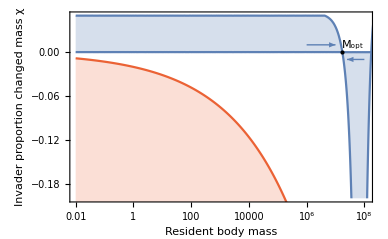

```mathematica
MinChi =Table[{Invade[[i]][[1]],Min[Invade[[i]][[2]]]},{i,1,Length[Invade]}];
MaxChi =Table[{Invade[[i]][[1]],Max[Invade[[i]][[2]]]},{i,1,Length[Invade]}];
InvasionPlot=Show[{
ListLogLinearPlot[{MinChi,MaxChi},Filling->{1->{2}},FillingStyle->Directive[ColorData[97,1],Opacity[0.25]],Joined->True,PlotRange->{{10^(-2),1.2*10^8},{-0.2,0.05}},PlotStyle->ColorData[97,1],Frame->True,FrameLabel->{"Resident body mass","Invader proportion changed mass χ"}],
ListLogLinearPlot[StarvationThreshold,Joined->True,PlotRange->{-1,0},PlotStyle->ColorData[97,4],Filling->Bottom],
Graphics[{PointSize[Large],Point[{Log@(1.73*10^7),0}]}],
Graphics[Text["M_opt",{Log@(4*10^7),0.01}]],
Graphics[{ColorData[97,1],Thick,Arrow[{{Log@(10^6),0.01},{Log@(10^7),0.01}}]}],
Graphics[{ColorData[97,1],Thick,Arrow[{{Log@(10^8),-0.01},{Log@(10^7.4),-0.01}}]}]
}]
```

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/Revision_2017/fig_Invasion5.pdf"}],InvasionPlot,"PDF",ImageResolution->800]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/Revision_2017/fig_Invasion5.pdf

```mathematica
Sort[MaxChi,#1[[2]]<#2[[2]]&]
```

{{3981.07,-∞},{3890.45,-∞},{2.88403×10^6,-0.000997637},{2.88403×10^8,-0.000996357},{7.58578×10^8,-0.000995137},{3.01995×10^6,-0.000994397},{213796.,-0.000994269},{7.4131×10^6,-0.000991739},{691831.,-0.000986842},{9.77237×10^6,-0.000983083},{16595.9,-0.00098273},{8.12831×10^8,-0.000981724},{2.29087×10^8,-0.000981263},{2.63027×10^7,-0.000980894},{1.×10^9,-0.000979996},{2.39883×10^7,-0.000977915},{2.23872×10^6,-0.00097606},{53703.2,-0.000974724},{12882.5,-0.000969535},{5.49541×10^7,-0.000968437},{6456.54,-0.000967383},{9.77237×10^7,-0.000964945},{4.0738×10^7,-0.000963983},{173780.,-0.000963795},{4.67735×10^7,-0.000963746},{19498.4,-0.000962754},{6.16595×10^6,-0.000959311},{9.54993×10^8,-0.000954895},{3.46737×10^7,-0.000954714},{3.89045×10^6,-0.000953593},{63095.7,-0.000949639},{562341.,-0.00094898},{1.99526×10^6,-0.000944539},{2.13796×10^7,-0.0009435},{6.91831×10^8,-0.000942711},{6.76083×10^7,-0.000942477},{5011.87,-0.000941582},{1.31826×10^8,-0.000938726},{4.36516×10^6,-0.000936284},{1.7378×10^8,-0.000935942},{147911.,-0.000932845},{33113.1,-0.000932281},{4.2658×10^7,-0.00092022},{4.46684×10^7,-0.000920013},{6.0256×10^8,-0.000917118},{6.76083×10^6,-0.000914136},{27542.3,-0.0009131},{91201.1,-0.000909587},{128825.,-0.000908443},{6760.83,-0.000907435},{12302.7,-0.000906979},{218776.,-0.000906219},{7.4131×10^7,-0.000904386},{794328.,-0.000901718},{4.46684×10^8,-0.000896855},{1.8197×10^7,-0.000895262},{50118.7,-0.000888817},{1.×10^8,-0.000884865},{21877.6,-0.000881184},{8.31764×10^7,-0.000879305},{2.75423×10^8,-0.000870255},{1.×10^7,-0.000868342},{15848.9,-0.000867788},{1.31826×10^6,-0.000867372},{3.89045×10^8,-0.000867362},{4265.8,-0.000867003},{24547.1,-0.000864157},{2.39883×10^8,-0.000862271},{69183.1,-0.000861604},{1.28825×10^8,-0.000861418},{1.54882×10^8,-0.000861004},{35481.3,-0.000860227},{549541.,-0.000857864},{7079.46,-0.000855749},{5.88844×10^7,-0.000855131},{11749.,-0.000853679},{676083.,-0.000851907},{3.54813×10^8,-0.000846799},{6.30957×10^7,-0.000846019},{8.51138×10^6,-0.000843104},{83176.4,-0.000840663},{177828.,-0.000840535},{1.×10^6,-0.000837621},{5248.07,-0.000837467},{2.81838×10^7,-0.000837276},{2.34423×10^6,-0.00083202},{46773.5,-0.000830107},{75857.8,-0.000824976},{3.23594×10^7,-0.000822981},{5.7544×10^6,-0.000822483},{223872.,-0.000822168},{102329.,-0.000822042},{114815.,-0.000821023},{1.02329×10^8,-0.000817588},{38018.9,-0.000813645},{18620.9,-0.00081314},{7413.1,-0.000812396},{4.67735×10^6,-0.000810391},{5.88844×10^8,-0.00080968},{11220.2,-0.000809555},{3.71535×10^6,-0.00080909},{2.63027×10^8,-0.000806233},{891251.,-0.000804399},{2.51189×10^8,-0.00080375},{3.0903×10^8,-0.000803105},{1.86209×10^6,-0.000798866},{58884.4,-0.000798864},{43651.6,-0.000798241},{1.25893×10^8,-0.000797543},{4.57088×10^8,-0.000794219},{40738.,-0.000792869},{3.01995×10^7,-0.00078424},{151356.,-0.000783143},{1.77828×10^7,-0.000782887},{7.58578×10^6,-0.000780577},{7762.47,-0.000777451},{29512.1,-0.000774737},{10715.2,-0.000774527},{2.13796×10^8,-0.000771985},{537032.,-0.000771511},{1.20226×10^6,-0.000769532},{5.24807×10^7,-0.000767854},{2.0893×10^7,-0.000765434},{1.04713×10^8,-0.000763169},{15135.6,-0.00076256},{1.02329×10^7,-0.000761867},{3.63078×10^7,-0.000761469},{1.09648×10^6,-0.000760127},{5.37032×10^6,-0.000752634},{3.31131×10^8,-0.000752624},{2.34423×10^7,-0.00075168},{1.86209×10^8,-0.000751049},{8128.31,-0.000750987},{1.41254×10^6,-0.000749725},{5.01187×10^6,-0.000748891},{10232.9,-0.000748516},{1.23027×10^8,-0.000747043},{229087.,-0.000742132},{5495.41,-0.000741224},{2.0893×10^6,-0.000738704},{131826.,-0.000736712},{776247.,-0.000736597},{4466.84,-0.000735867},{8.51138×10^8,-0.000734626},{8511.38,-0.000733079},{9772.37,-0.000731443},{6.76083×10^8,-0.000726027},{8912.51,-0.000723802},{9332.54,-0.000723231},{4.16869×10^6,-0.000722239},{660693.,-0.000721927},{1.07152×10^8,-0.000721665},{181970.,-0.000721119},{5.7544×10^8,-0.000720172},{2.5704×10^7,-0.000715357},{2.45471×10^6,-0.000713078},{8.51138×10^7,-0.00071116},{1.20226×10^8,-0.00070986},{4.67735×10^8,-0.000708671},{1.7378×10^6,-0.000707248},{20893.,-0.000706146},{7.4131×10^8,-0.000704014},{1.99526×10^8,-0.000695826},{1.09648×10^8,-0.000693133},{1.69824×10^8,-0.000692763},{3.54813×10^6,-0.000691981},{524807.,-0.0006899},{1.51356×10^8,-0.000687997},{6.30957×10^6,-0.000686624},{1.1749×10^8,-0.000685935},{26302.7,-0.000685514},{93325.4,-0.000685247},{1.51356×10^6,-0.000683369},{1.7378×10^7,-0.000679733},{8.70964×10^6,-0.00067952},{1.12202×10^8,-0.000677629},{54954.1,-0.000676132},{1.14815×10^8,-0.000675211},{7.58578×10^7,-0.000674967},{17782.8,-0.000673541},{64565.4,-0.00067286},{6.91831×10^6,-0.000671942},{1.62181×10^6,-0.000668981},{14454.4,-0.00066696},{234423.,-0.00066613},{6.91831×10^7,-0.000664996},{3.98107×10^8,-0.000663753},{1.04713×10^7,-0.000663694},{23442.3,-0.000663132},{31622.8,-0.000660969},{5754.4,-0.000652925},{5.62341×10^8,-0.000648517},{4.7863×10^8,-0.000640286},{154882.,-0.000637169},{7.94328×10^8,-0.00063391},{117490.,-0.00063137},{977237.,-0.000620396},{2.5704×10^6,-0.000619456},{104713.,-0.000614855},{870964.,-0.000613511},{512861.,-0.000613011},{5.01187×10^7,-0.000612576},{4677.35,-0.000612368},{3.80189×10^7,-0.000610468},{186209.,-0.000605565},{85113.8,-0.000602867},{3.38844×10^6,-0.000602026},{70794.6,-0.000597593},{645654.,-0.000596879},{2.04174×10^7,-0.000596877},{5.49541×10^8,-0.000594636},{239883.,-0.000594179},{4.89779×10^8,-0.00058914},{5.62341×10^7,-0.000585842},{1.69824×10^7,-0.00058576},{1.28825×10^6,-0.000584537},{2.95121×10^8,-0.000582858},{51286.1,-0.000581079},{13803.8,-0.000580904},{3.63078×10^8,-0.000577333},{7.76247×10^6,-0.000577258},{758578.,-0.000576562},{77624.7,-0.000573958},{1.07152×10^7,-0.000573859},{6025.6,-0.000572637},{33884.4,-0.00057212},{134896.,-0.000568611},{3.38844×10^7,-0.000567062},{8.91251×10^8,-0.00056445},{2.23872×10^8,-0.000563271},{5.37032×10^8,-0.000558451},{2.18776×10^6,-0.000557424},{1.94984×10^6,-0.000556598},{8.70964×10^7,-0.000555431},{5.01187×10^8,-0.000555307},{4.46684×10^6,-0.000553884},{2.69153×10^6,-0.000551375},{16982.4,-0.00054387},{2.75423×10^7,-0.000541809},{19952.6,-0.000541344},{501187.,-0.000540823},{5.24807×10^8,-0.000539886},{3.23594×10^6,-0.000538991},{5.12861×10^8,-0.000538864},{3.98107×10^6,-0.000536193},{2.29087×10^7,-0.000535164},{6.45654×10^7,-0.00053304},{28183.8,-0.000530933},{1.47911×10^8,-0.000528841},{6.60693×10^8,-0.000527751},{5.88844×10^6,-0.000527274},{245471.,-0.000526297},{8.91251×10^6,-0.000523987},{1.07152×10^6,-0.000521413},{47863.,-0.000513344},{60256.,-0.000512655},{2.81838×10^6,-0.000509061},{1.1749×10^6,-0.000508951},{36307.8,-0.00050852},{6.0256×10^7,-0.000507116},{13182.6,-0.00050431},{3.0903×10^6,-0.000502639},{4.7863×10^7,-0.00050221},{3.98107×10^7,-0.00050208},{1.65959×10^7,-0.000500929},{6309.57,-0.000500432},{4897.79,-0.000496571},{158489.,-0.000494939},{190546.,-0.000493888},{2.95121×10^6,-0.00049274},{1.09648×10^7,-0.0004924},{4.0738×10^8,-0.00047679},{630957.,-0.000476742},{489779.,-0.000473315},{22387.2,-0.00047257},{44668.4,-0.000472569},{9.33254×10^8,-0.000471872},{38904.5,-0.000470502},{25118.9,-0.000468622},{3.16228×10^7,-0.000466462},{1.8197×10^8,-0.000465023},{95499.3,-0.000464307},{1.65959×10^8,-0.000463741},{251189.,-0.000462503},{2.51189×10^7,-0.000459711},{2.95121×10^7,-0.000458447},{41686.9,-0.000458404},{7.76247×10^7,-0.000457697},{9.77237×10^8,-0.000457574},{1.38038×10^6,-0.000449942},{4.7863×10^6,-0.000449361},{120226.,-0.00044527},{1.99526×10^7,-0.000437785},{7.07946×10^6,-0.000437456},{12589.3,-0.000437095},{3.16228×10^8,-0.000436989},{4.16869×10^7,-0.000436681},{6606.93,-0.000436381},{4.57088×10^7,-0.000436363},{4168.69,-0.000435413},{5.49541×10^6,-0.000435196},{3.38844×10^8,-0.000434515},{7.24436×10^8,-0.000431623},{1.8197×10^6,-0.000429022},{851138.,-0.000427821},{2.81838×10^8,-0.000425512},{1.62181×10^7,-0.000425198},{16218.1,-0.00042404},{741310.,-0.000421592},{6.45654×10^6,-0.00042151},{1.12202×10^7,-0.000419353},{4.36516×10^7,-0.000414648},{2.34423×10^8,-0.000414241},{8.91251×10^7,-0.000412173},{107152.,-0.000411145},{478630.,-0.000410468},{5.12861×10^6,-0.000409513},{954993.,-0.000408484},{138038.,-0.000404159},{257040.,-0.000402812},{2.29087×10^6,-0.000400916},{30199.5,-0.000400732},{7.07946×10^7,-0.000399452},{66069.3,-0.000399252},{2.0893×10^8,-0.000398561},{5128.61,-0.000388545},{19054.6,-0.000386689},{194984.,-0.000386106},{1.44544×10^8,-0.000383477},{7.94328×10^6,-0.000381817},{56234.1,-0.000380616},{6918.31,-0.000380555},{12022.6,-0.000379177},{3.80189×10^6,-0.000377902},{9.12011×10^6,-0.000376542},{87096.4,-0.000368412},{1.47911×10^6,-0.000366414},{1.94984×10^8,-0.000366387},{5.37032×10^7,-0.000362457},{616595.,-0.000361495},{1.58489×10^7,-0.000358529},{162181.,-0.00035647},{1.69824×10^6,-0.000355266},{1.14815×10^7,-0.000354754},{3.54813×10^7,-0.000352834},{467735.,-0.00035226},{8.31764×10^8,-0.000348602},{6.45654×10^8,-0.000347802},{263027.,-0.000347245},{2.04174×10^6,-0.000338565},{72443.6,-0.000336808},{1.58489×10^6,-0.000334627},{7244.36,-0.000333026},{2.69153×10^8,-0.000330518},{11481.5,-0.000330475},{2.23872×10^7,-0.000328323},{79432.8,-0.000326223},{4.2658×10^6,-0.000325746},{2.45471×10^8,-0.000325418},{3.71535×10^8,-0.000324224},{15488.2,-0.000313965},{1.25893×10^6,-0.000307301},{4.16869×10^8,-0.000306545},{7.76247×10^8,-0.000305075},{1.54882×10^7,-0.000300881},{4365.16,-0.000300485},{457088.,-0.000298671},{1.1749×10^7,-0.000298641},{26915.3,-0.000297964},{2.5704×10^8,-0.000297333},{269153.,-0.000295819},{32359.4,-0.000295234},{7585.78,-0.000293868},{21379.6,-0.00029238},{10964.8,-0.000290909},{5370.32,-0.000288357},{1.94984×10^7,-0.000288119},{1.04713×10^6,-0.000288106},{199526.,-0.000282236},{9.12011×10^7,-0.000281441},{52480.7,-0.000276377},{724436.,-0.000271663},{2.39883×10^6,-0.000269398},{7943.28,-0.000263155},{123027.,-0.000262738},{23988.3,-0.000262331},{10471.3,-0.000260399},{2.69153×10^7,-0.000256363},{1.14815×10^6,-0.000253872},{7.94328×10^7,-0.000252628},{1.51356×10^7,-0.000252216},{1.41254×10^8,-0.000251843},{602560.,-0.000251117},{1.20226×10^7,-0.000251051},{446684.,-0.000249682},{1.62181×10^8,-0.000248814},{275423.,-0.000248551},{831764.,-0.000247308},{3.63078×10^6,-0.000247126},{97723.7,-0.000246783},{141254.,-0.000243369},{18197.,-0.000242094},{8317.64,-0.000240959},{6.0256×10^6,-0.000239539},{10000.,-0.000238867},{9.33254×10^6,-0.000237219},{6.60693×10^7,-0.000231842},{61659.5,-0.000229575},{8709.64,-0.000227357},{9549.93,-0.000226234},{9120.11,-0.000222423},{165959.,-0.000221779},{34673.7,-0.000214765},{5.7544×10^7,-0.000214724},{2.45471×10^7,-0.000213911},{14791.1,-0.000213562},{1.47911×10^7,-0.000212494},{1.23027×10^7,-0.000212021},{109648.,-0.000210926},{7.24436×10^6,-0.00021071},{281838.,-0.000205461},{436516.,-0.000205272},{933254.,-0.000201863},{48977.9,-0.000199576},{5623.41,-0.000196077},{8.12831×10^6,-0.000194287},{1.77828×10^8,-0.000193342},{3.31131×10^7,-0.000189833},{6.30957×10^8,-0.000186099},{3.01995×10^8,-0.000185085},{5.12861×10^7,-0.000184576},{204174.,-0.000182295},{1.44544×10^7,-0.000181676},{1.25893×10^7,-0.000181589},{3.71535×10^7,-0.000180665},{4.57088×10^6,-0.000178576},{7.07946×10^8,-0.000177882},{1.90546×10^6,-0.000174715},{4570.88,-0.000173159},{6.16595×10^7,-0.000170728},{288403.,-0.000166566},{426580.,-0.000165421},{6.60693×10^6,-0.000164003},{9.33254×10^7,-0.000163288},{2.51189×10^6,-0.000163088},{2.18776×10^8,-0.0001602},{1.28825×10^7,-0.000159793},{1.41254×10^7,-0.000159723},{37153.5,-0.000159655},{1.34896×10^6,-0.000155832},{4.2658×10^8,-0.000153092},{28840.3,-0.000151475},{45708.8,-0.000149853},{1.90546×10^7,-0.000147837},{1.31826×10^7,-0.00014667},{1.38038×10^7,-0.000146597},{7.24436×10^7,-0.000145898},{588844.,-0.000145586},{2.13796×10^6,-0.000144981},{3.46737×10^6,-0.000143624},{2.88403×10^7,-0.000142807},{1.34896×10^7,-0.000142258},{8.70964×10^8,-0.00013988},{89125.1,-0.000137314},{1.38038×10^8,-0.000133879},{3.46737×10^8,-0.00013255},{295121.,-0.000131886},{2.18776×10^7,-0.000131116},{39810.7,-0.000130239},{416869.,-0.00013011},{67608.3,-0.000128829},{42658.,-0.000126857},{707946.,-0.000126754},{4.0738×10^6,-0.000125731},{5.62341×10^6,-0.000125135},{14125.4,-0.000122744},{20417.4,-0.000122471},{3.0903×10^7,-0.00012023},{5888.44,-0.000111775},{17378.,-0.00010747},{9.54993×10^6,-0.000106054},{301995.,-0.000101438},{407380.,-0.0000993181},{4.89779×10^6,-0.000095517},{169824.,-0.0000908815},{57544.,-0.0000881888},{3.80189×10^8,-0.0000875426},{3.23594×10^8,-0.0000868049},{208930.,-0.0000863004},{144544.,-0.0000862595},{125893.,-0.0000837908},{2.63027×10^6,-0.0000822087},{81283.1,-0.0000817866},{74131.,-0.0000792646},{5.24807×10^6,-0.0000774173},{25704.,-0.0000757368},{309030.,-0.0000752403},{398107.,-0.0000730259},{812831.,-0.0000719475},{3.31131×10^6,-0.0000671585},{22908.7,-0.0000665488},{1.77828×10^6,-0.0000651583},{1.02329×10^6,-0.0000601838},{8.12831×10^7,-0.0000598123},{9.54993×10^7,-0.0000577712},{1.44544×10^6,-0.0000552076},{4786.3,-0.0000535022},{316228.,-0.0000533127},{4.89779×10^7,-0.0000518037},{1.90546×10^8,-0.0000514827},{389045.,-0.0000512139},{3.89045×10^7,-0.0000509238},{1.58489×10^8,-0.0000479225},{575440.,-0.0000448806},{6.16595×10^8,-0.0000425644},{13489.6,-0.0000414299},{2.04174×10^8,-0.0000398621},{323594.,-0.0000356734},{1.23027×10^6,-0.000035641},{6165.95,-0.0000355197},{380189.,-0.0000338625},{100000.,-0.0000326895},{1.34896×10^8,-0.0000295269},{30903.,-0.0000294723},{2.75423×10^6,-0.0000269832},{331131.,-0.0000223414},{371535.,-0.0000209521},{3.16228×10^6,-0.0000174942},{1.86209×10^7,-0.0000168983},{4.36516×10^8,-0.0000165037},{8.31764×10^6,-0.0000147049},{112202.,-0.0000142134},{338844.,-0.0000133353},{363078.,-0.0000124635},{1.65959×10^6,-9.18549×10^-6},{346737.,-8.67427×10^-6},{9.12011×10^8,-8.4185×10^-6},{354813.,-8.3773×10^-6},{1.54882×10^6,-6.09847×10^-6},{4073.8,-5.70779×10^-6},{1.12202×10^6,-4.27176×10^-6},{912011.,-5.08908×10^-7},{3801.89,0.000272187},{3715.35,0.000694438},{3630.78,0.00111485},{3548.13,0.00153342},{3467.37,0.00195016},{3388.44,0.00236509},{3311.31,0.00277821},{3235.94,0.00318952},{3162.28,0.00359903},{3090.3,0.00400676},{2884.03,0.0042193},{3019.95,0.00441271},{2818.38,0.00461995},{2951.21,0.00481689},{2754.23,0.00501886},{2691.53,0.00541603},{2630.27,0.00581146},{2570.4,0.00620516},{2511.89,0.00659715},{2454.71,0.00698742},{2398.83,0.007376},{2344.23,0.00776287},{2290.87,0.00814806},{2238.72,0.00853156},{2187.76,0.00891339},{2137.96,0.00929356},{2089.3,0.00967206},{2041.74,0.0100489},{1995.26,0.0104241},{1949.84,0.0107977},{1905.46,0.0111696},{1862.09,0.0115399},{1819.7,0.0119086},{1698.24,0.0120051},{1778.28,0.0122757},{1659.59,0.0123674},{1737.8,0.0126412},{1621.81,0.0127281},{1584.89,0.0130873},{1548.82,0.0134449},{1513.56,0.0138009},{1479.11,0.0141553},{1445.44,0.0145083},{1412.54,0.0148596},{1380.38,0.0152095},{1348.96,0.0155578},{1318.26,0.0159046},{1288.25,0.0162499},{1258.93,0.0165936},{1230.27,0.0169359},{1202.26,0.0172767},{1122.02,0.0172901},{1174.9,0.017616},{1096.48,0.017625},{1148.15,0.0179538},{1071.52,0.0179584},{1047.13,0.0182903},{1023.29,0.0186208},{1000.,0.0189499},{977.237,0.0192775},{954.993,0.0196037},{933.254,0.0199285},{912.011,0.0202518},{891.251,0.0205737},{870.964,0.0208943},{851.138,0.0212134},{776.247,0.0214761},{831.764,0.0215312},{758.578,0.0217883},{812.831,0.0218475},{741.31,0.0220992},{794.328,0.0221625},{724.436,0.0224087},{707.946,0.0227168},{691.831,0.0230236},{676.083,0.0233291},{660.693,0.0236332},{645.654,0.0239361},{630.957,0.0242375},{616.595,0.0245377},{602.56,0.0248366},{549.541,0.025019},{588.844,0.0251341},{537.032,0.0253114},{575.44,0.0254304},{524.807,0.0256026},{562.341,0.0257254},{512.861,0.0258924},{501.187,0.026181},{489.779,0.0264683},{478.63,0.0267544},{467.735,0.0270392},{457.088,0.0273228},{446.684,0.0276051},{407.38,0.0277222},{436.516,0.0278862},{398.107,0.0279984},{426.58,0.0281661},{389.045,0.0282735},{416.869,0.0284448},{380.189,0.0285473},{371.535,0.0288199},{363.078,0.0290913},{354.813,0.0293616},{346.737,0.0296307},{338.844,0.0298986},{331.131,0.0301653},{301.995,0.0302206},{323.594,0.0304309},{295.121,0.0304816},{316.228,0.0306953},{288.403,0.0307414},{309.03,0.0309585},{281.838,0.0310001},{275.423,0.0312576},{269.153,0.0315141},{263.027,0.0317694},{257.04,0.0320236},{251.189,0.0322767},{223.872,0.0325256},{245.471,0.0325287},{218.776,0.0327722},{239.883,0.0327795},{213.796,0.0330176},{234.423,0.0330293},{208.93,0.033262},{229.087,0.033278},{204.174,0.0335053},{199.526,0.0337476},{194.984,0.0339888},{190.546,0.0342289},{169.824,0.034414},{186.209,0.034468},{165.959,0.0346479},{181.97,0.0347061},{162.181,0.0348808},{177.828,0.0349431},{158.489,0.0351127},{173.78,0.035179},{154.882,0.0353436},{151.356,0.0355734},{147.911,0.0358023},{144.544,0.0360302},{128.825,0.0361546},{141.254,0.036257},{125.893,0.0363766},{138.038,0.0364829},{123.027,0.0365976},{134.896,0.0367078},{120.226,0.0368176},{131.826,0.0369317},{117.49,0.0370367},{114.815,0.0372548},{112.202,0.0374719},{109.648,0.0376881},{97.7237,0.0377551},{107.152,0.0379034},{95.4993,0.0379657},{104.713,0.0381177},{93.3254,0.0381754},{102.329,0.0383311},{91.2011,0.0383842},{100.,0.0385436},{89.1251,0.038592},{87.0964,0.038799},{85.1138,0.039005},{83.1764,0.0392102},{74.131,0.0392226},{81.2831,0.0394144},{72.4436,0.0394224},{79.4328,0.0396178},{70.7946,0.0396214},{69.1831,0.0398195},{77.6247,0.0398203},{67.6083,0.0400167},{75.8578,0.0400219},{66.0693,0.0402131},{57.544,0.0403734},{64.5654,0.0404086},{56.2341,0.0405638},{63.0957,0.0406032},{54.9541,0.0407535},{61.6595,0.040797},{53.7032,0.0409422},{60.256,0.04099},{52.4807,0.0411302},{58.8844,0.0411821},{51.2861,0.0413174},{50.1187,0.0415037},{43.6516,0.0416047},{48.9779,0.0416892},{42.658,0.0417854},{47.863,0.0418739},{41.6869,0.0419653},{46.7735,0.0420578},{40.738,0.0421444},{45.7088,0.0422409},{39.8107,0.0423228},{44.6684,0.0424232},{38.9045,0.0425003},{38.0189,0.0426771},{33.1131,0.0427218},{37.1535,0.0428532},{32.3594,0.0428933},{36.3078,0.0430284},{31.6228,0.043064},{35.4813,0.0432029},{30.903,0.043234},{34.6737,0.0433766},{30.1995,0.0434032},{33.8844,0.0435496},{29.5121,0.0435717},{25.1189,0.0437307},{28.8403,0.0437394},{24.5471,0.0438934},{28.1838,0.0439065},{23.9883,0.0440554},{27.5423,0.0440727},{23.4423,0.0442166},{26.9153,0.0442383},{22.9087,0.0443772},{26.3027,0.0444032},{22.3872,0.0445371},{25.704,0.0445673},{19.0546,0.0446368},{21.8776,0.0446963},{18.6209,0.0447912},{21.3796,0.0448547},{18.197,0.0449449},{20.893,0.0450125},{17.7828,0.0450979},{20.4174,0.0451696},{17.378,0.0452503},{19.9526,0.045326},{16.9824,0.045402},{14.4544,0.0454455},{19.4984,0.0454818},{16.5959,0.045553},{14.1254,0.0455919},{16.2181,0.0457034},{13.8038,0.0457378},{15.8489,0.0458531},{13.4896,0.045883},{15.4882,0.0460022},{13.1826,0.0460275},{15.1356,0.0461506},{10.9648,0.0461616},{12.8825,0.0461715},{14.7911,0.0462983},{10.7152,0.0463006},{12.5893,0.0463148},{10.4713,0.046439},{12.3027,0.0464575},{10.2329,0.0465767},{12.0226,0.0465995},{10.,0.0467139},{11.749,0.046741},{8.31764,0.04679},{9.77237,0.0468505},{11.4815,0.0468818},{8.12831,0.0469218},{9.54993,0.0469865},{11.2202,0.047022},{7.94328,0.0470531},{9.33254,0.0471218},{7.76247,0.0471839},{9.12011,0.0472566},{7.58578,0.047314},{8.91251,0.0473908},{7.4131,0.0474436},{6.16595,0.0474602},{8.70964,0.0475245},{7.24436,0.0475726},{6.0256,0.0475848},{8.51138,0.0476575},{7.07946,0.0477011},{5.88844,0.0477088},{6.91831,0.047829},{5.7544,0.0478323},{4.67735,0.0479198},{5.62341,0.0479553},{6.76083,0.0479563},{4.57088,0.048038},{5.49541,0.0480777},{6.60693,0.0480831},{4.46684,0.0481557},{5.37032,0.0481996},{6.45654,0.0482094},{4.36516,0.0482729},{5.24807,0.0483209},{6.30957,0.048335},{4.2658,0.0483896},{5.12861,0.0484418},{4.16869,0.0485058},{3.38844,0.0485287},{5.01187,0.0485621},{4.0738,0.0486214},{3.31131,0.0486399},{4.89779,0.0486818},{3.98107,0.0487366},{3.23594,0.0487506},{4.7863,0.0488011},{3.89045,0.0488512},{3.16228,0.0488608},{2.51189,0.0489369},{3.80189,0.0489654},{3.0903,0.0489705},{0.724436,0.0490001},{0.040738,0.0490036},{0.0141254,0.0490081},{0.144544,0.0490121},{0.0245471,0.0490126},{0.0977237,0.0490147},{2.45471,0.049042},{0.398107,0.0490429},{0.0138038,0.0490474},{1.54882,0.0490491},{0.288403,0.0490503},{0.0630957,0.0490505},{0.537032,0.0490505},{0.0398107,0.0490516},{0.0239883,0.0490562},{0.933254,0.0490634},{0.204174,0.0490634},{1.94984,0.0490675},{0.0954993,0.0490714},{0.141254,0.0490732},{3.71535,0.049079},{3.01995,0.0490798},{1.20226,0.0490805},{0.707946,0.049083},{0.0134896,0.0490864},{0.0389045,0.0490994},{0.0234423,0.0490996},{0.0616595,0.0491026},{0.389045,0.0491169},{0.281838,0.04912},{0.0131826,0.0491253},{0.0933254,0.0491278},{0.199526,0.0491286},{0.524807,0.0491289},{0.138038,0.049134},{0.0229087,0.0491428},{1.51356,0.049145},{2.39883,0.0491465},{0.0380189,0.049147},{0.912011,0.0491504},{0.060256,0.0491546},{0.0128825,0.0491641},{0.691831,0.0491656},{1.90546,0.0491676},{1.1749,0.0491718},{0.0912011,0.049184},{0.0223872,0.0491859},{2.95121,0.0491886},{0.275423,0.0491893},{0.380189,0.0491906},{3.63078,0.0491922},{0.194984,0.0491935},{0.0371535,0.0491943},{0.134896,0.0491945},{0.0125893,0.0492027},{0.0588844,0.0492063},{0.512861,0.0492069},{0.0218776,0.0492287},{0.891251,0.0492371},{0.0891251,0.04924},{1.47911,0.0492404},{0.0123027,0.0492411},{0.0363078,0.0492415},{0.676083,0.0492478},{2.34423,0.0492507},{0.131826,0.0492548},{0.057544,0.0492577},{0.190546,0.0492582},{0.269153,0.0492583},{1.14815,0.0492627},{0.371535,0.049264},{1.86209,0.0492673},{0.0213796,0.0492714},{0.0120226,0.0492793},{0.501187,0.0492846},{0.0354813,0.0492885},{0.0870964,0.0492957},{2.88403,0.0492969},{3.54813,0.0493048},{0.0562341,0.049309},{0.020893,0.0493138},{0.128825,0.0493148},{0.011749,0.0493174},{0.186209,0.0493225},{0.870964,0.0493233},{0.263027,0.049327},{0.660693,0.0493297},{0.0346737,0.0493352},{1.44544,0.0493354},{0.363078,0.0493371},{0.0851138,0.0493511},{1.12202,0.0493533},{2.29087,0.0493543},{0.0114815,0.0493553},{0.0204174,0.0493561},{0.0549541,0.04936},{0.489779,0.0493619},{1.8197,0.0493665},{0.125893,0.0493745},{0.0338844,0.0493818},{0.18197,0.0493866},{0.0112202,0.049393},{0.25704,0.0493954},{0.0199526,0.0493982},{2.81838,0.0494047},{0.0831764,0.0494064},{0.851138,0.0494092},{0.354813,0.0494098},{0.0537032,0.0494109},{0.645654,0.0494112},{3.46737,0.049417},{0.0331131,0.0494281},{1.41254,0.0494299},{0.0109648,0.0494306},{0.123027,0.049434},{0.47863,0.0494389},{0.0194984,0.0494401},{1.09648,0.0494434},{0.177828,0.0494504},{2.23872,0.0494576},{0.0812831,0.0494613},{0.0524807,0.0494614},{0.251189,0.0494636},{1.77828,0.0494653},{0.0107152,0.049468},{0.0323594,0.0494743},{0.0190546,0.0494819},{0.346737,0.0494822},{0.630957,0.0494923},{0.120226,0.0494932},{0.831764,0.0494948},{0.0104713,0.0495052},{0.0512861,0.0495118},{2.75423,0.0495121},{0.17378,0.0495139},{0.467735,0.0495156},{0.0794328,0.0495161},{0.0316228,0.0495202},{0.0186209,0.0495234},{1.38038,0.0495241},{0.245471,0.0495314},{1.07152,0.0495331},{0.0102329,0.0495423},{0.11749,0.0495522},{0.338844,0.0495543},{2.18776,0.0495603},{0.0501187,0.049562},{1.7378,0.0495637},{0.018197,0.0495648},{0.030903,0.049566},{0.0776247,0.0495706},{0.616595,0.0495731},{0.169824,0.0495771},{0.01,0.0495792},{0.812831,0.0495799},{0.457088,0.0495919},{0.239883,0.0495989},{0.0177828,0.049606},{0.114815,0.0496109},{0.0301995,0.0496115},{0.0489779,0.0496119},{1.34896,0.0496179},{2.69153,0.049619},{1.04713,0.0496225},{0.0758578,0.0496248},{0.331131,0.0496261},{0.165959,0.0496401},{0.017378,0.049647},{0.60256,0.0496536},{0.0295121,0.0496569},{0.047863,0.0496616},{1.69824,0.0496616},{2.13796,0.0496627},{0.794328,0.0496647},{0.234423,0.0496661},{0.446684,0.0496679},{0.112202,0.0496693},{0.074131,0.0496788},{0.0169824,0.0496878},{0.323594,0.0496976},{0.0288403,0.049702},{0.162181,0.0497028},{0.0467735,0.0497111},{1.31826,0.0497112},{1.02329,0.0497114},{2.63027,0.0497254},{0.109648,0.0497275},{0.0165959,0.0497285},{0.0724436,0.0497326},{0.229087,0.0497331},{0.588844,0.0497337},{0.436516,0.0497436},{0.0281838,0.049747},{0.776247,0.0497491},{1.65959,0.0497592},{0.0457088,0.0497604},{2.0893,0.0497645},{0.158489,0.0497652},{0.316228,0.0497688},{0.0162181,0.0497689},{0.107152,0.0497855},{0.0707946,0.0497862},{0.0275423,0.0497917},{0.223872,0.0497997},{1.,0.0498},{1.28825,0.0498041},{0.0158489,0.0498092},{0.0446684,0.0498095},{0.57544,0.0498134},{0.42658,0.0498189},{0.154882,0.0498273},{2.5704,0.0498314},{0.758578,0.0498331},{0.0269153,0.0498363},{0.0691831,0.0498395},{0.30903,0.0498396},{0.104713,0.0498432},{0.0154882,0.0498494},{1.62181,0.0498562},{0.0436516,0.0498583},{2.04174,0.049866},{0.218776,0.0498661},{0.0263027,0.0498807},{0.977237,0.0498882},{0.151356,0.0498892},{0.0151356,0.0498893},{0.0676083,0.0498926},{0.562341,0.0498928},{0.416869,0.0498939},{1.25893,0.0498967},{0.102329,0.0499006},{0.042658,0.0499069},{0.301995,0.0499102},{0.74131,0.0499168},{0.025704,0.0499249},{0.0147911,0.0499291},{0.213796,0.0499321},{0.0660693,0.0499454},{0.147911,0.0499508},{1.58489,0.0499529},{0.0416869,0.0499554},{0.1,0.0499578},{1.99526,0.049967},{0.40738,0.0499686},{0.0144544,0.0499687},{0.0251189,0.0499688},{0.549541,0.0499718},{0.954993,0.049976},{0.295121,0.0499804},{1.23027,0.0499888},{0.20893,0.0499979},{0.0645654,0.0499981}}

```mathematica
data = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/mathematica/NewRateFigures_Final/densitydata.csv"}],"csv"];
```

```mathematica
Log10@3981.071705534969
```

3.6

```mathematica
Median[Log10@data[[All,1]]]
Mean[Log10@data[[All,1]]]
```

3.0086

3.06209

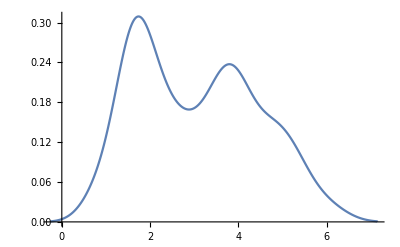

```mathematica
SmoothHistogram[Log10@data[[All,1]]]
```

```mathematica
mm=Table[10^x,{x,0,8,0.001}];
```

```mathematica
mm[[6927]]
```

8.43335×10^6

```mathematica
MinBM=Table[{(10^MassExp),(1+MinMass)*(10^MassExp)^1.19},{MassExp,-2,9,0.01}];
MaxBM=Table[{10^MassExp,MinMass*10^MassExp},{MassExp,-2,9,0.01}]
```

{{0.01,{{0.0001,5.79238×10^-6},{0.000102329,5.42318×10^-6},{0.000104713,5.05235×10^-6},{0.000107152,4.6799×10^-6},1093,{9.33254×10^6,-0.00217472},{9.54993×10^6,-0.00238955},{9.77237×10^6,-0.00259458},{1.×10^7,-0.0028098}}},1099,{1.×10^9,{1}}}
 |  |  |  |

```mathematica
Show[{
ListLogLogPlot[MinBM],
ListLogLogPlot[MaxBM]
}]
```

-Graphics-